# Chapter. Potential sweep methods

## Non-reversible reactions

In this notebook you are asked to load data from the SERM/Data folder. To prepare for this copy the line below to an input cell, replace the file path with the file path for the "Data" folder on your computer and press ⌤
AppendTo[$Path,”(* path to *)/SERM/Data/chapter6”];
AppendTo[$Path,”(* path to *)/SERM/Data/DigiSimdata”];
or
AppendTo[$Path,ToFileName[ {NotebookDirectory[],”Data”,”chapter6”}]];
AppendTo[$Path,ToFileName[ {NotebookDirectory[],”Data”,”DigiSimdata”}]];

Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->100,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12],Cell[TextData[{"Potential sweep methods"}],FontFamily->"Arial",FontSize->12],None},
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Irreversible reactions","Numerical solution of the Volterra equation of the second kind","Numerical solutions to the Volterra equation","Finite difference solutions for quasi reversible reactions","Summary","Further Reading"},#]&)]],FontFamily->"Arial",FontSize->12], Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12]}},

PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"GraphicsPrintingFormat"->"DownloadPostScript",
"FirstPageFace"->Right,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
Needs["Notation`"];
```

```mathematica
ClearNotations[]
Symbolize[c^_];
Symbolize[Subscript[r, _]];
Symbolize[Subscript[c, _]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
BaseStyle->{FontFamily-> "Arial",FontSize-> 10, FontWeight->Plain},
FrameLabel->None,
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},
FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
(* tick function for labelled axes or frames *)
ticks1[min_,max_,steps_,divs_]:=Join[Table[{x,Which[
Chop[x]==0,0,
0<x<2,NumberForm[x,{2,2},NumberPadding->{"","0"}],
x≥2,NumberForm[x,{2,0},NumberPadding->{"","0"}],
0>x≥-2,NumberForm[x,{2,2},NumberPadding->{"0","0"}],
-2>x,NumberForm[x,{2,0},NumberPadding->{"","0"}]
],{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]];

(* tick function for non-labelled axes or frames *)
ticks2[min_,max_,steps_,divs_]:=Chop[Join[Table[{x,"",{0.015,0}},{x,min,max,steps}],Table[{x,"",{0.0075,0}},{x,min,max,steps/divs}]]];
```

```mathematica
optionA={
PlotStyle-> {Black,AbsoluteThickness[0.5]},
FrameTicks->{ticks1[-30,10,5,5],ticks1[.6,-.6,-.2,5],ticks2[-30,10,5,5],ticks2[.6,-.6,-.2,5]},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic,10],
Style["√πχ",FontFamily-> "Times New Roman",10],
None,
None}
};
```

```mathematica
optionA2={
FrameTicks->{ticks1[-50,10,10,5],ticks1[.6,-1.2,-.2,5],ticks2[-50,10,10,5],ticks2[.6,-1.2,-.2,5]},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",Italic,10],
Style["√πχ",FontFamily-> "Times New Roman",10],
None,
None},
PlotStyle-> {Black,AbsoluteThickness[0.5]}
};
```

```mathematica
optionB={
Axes-> False,
FrameTicks->{ticks1[-50,20,10,5],ticks1[.5,-.5,-.1,5],ticks2[-50,20,10,5],ticks2[.5,-.5,-.1,5]},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",10, FontSlant->Italic],
Style["√πχ",FontFamily-> "Times New Roman",10],
None,
None},
PlotRange-> {{14., -26.}, {-0.4,0.1}},
PlotStyle-> {Black,AbsoluteThickness[.5]}};
```

```mathematica
ClearAll[LowerDiagonalMatrix,UpperDiagonalMatrix];

LowerDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#≥#2,f[##],0]&,{n,n}];

UpperDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#≤#2,f[##],0]&,{n,n}];
```

```mathematica
ClearAll[f,F,R,T,𝒟,α];

F=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","FaradayConstant"],"Value"];(*Faradays constant*)
R=N@QuantityMagnitude@EntityValue[Entity["PhysicalConstant","MolarGasConstant"],"Value"];(*gas constant*)
T = 298.; (*Absolute temperature*)
f=F/(R*T);
𝒟=1.*10^-5;(*diffusion coefficient of substrate in cm^2 s^-1*)
α=0.5; (*transfer coefficient*)

(* this function is used to convert DigiSim data to a dimensionless scale *)

convert[list_List]:=Module[{f=38.9413, A=1., 𝒟=1.*^-5, υ=1., c1=1.*^-6, values},
values=F*A*c1*Sqrt[𝒟*f*υ];
Map[{#⟦1⟧*f,-#⟦2⟧/values}&,list]
]
```

```mathematica
Unprotect[InverseLaplaceTransform];
InverseLaplaceTransform[i_[s]/(√s), s_, t_] := 1/(√π)*∫_0^t i[τ]/(√(t-τ))ⅆτ;

Protect[InverseLaplaceTransform];
```

This for Mathematica Version 4.0 and above

```mathematica
If[$VersionNumber>3.,
Unprotect[LaplaceTransform];

LaplaceTransform[Derivative[d__][c][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][C[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][u][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][U[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[Derivative[d__][v][args__],t_,s_]:=With[{pos=Position[{args},t]},Derivative[Sequence@@Delete[{d},pos⟦1,1⟧]][V[s]][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1&&{d}[[pos⟦1,1⟧]]===0];
LaplaceTransform[c[args__],t_,s_]:=With[{pos=Position[{args},t]},C[s][Sequence@@(Delete[{args},pos⟦1,1⟧]/.t->s)]/;Length[pos]===1]

(*Protect[LaplaceTransform];*)];
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

In the preceding chapter we used the analytical methods outlined in Chapter 1 to develop a symbolic solution for reversible linear sweep and cyclic voltammetry. The result could be solved numerically using NIntegrate. In this chapter we extend both the analytical and numerical approach to the voltammetry of irreversible and quasi-reversible reactions.

## Chapter.Section Irreversible reactions

To derive the equation for the cyclic voltammogram of irreversible reactions we begin with the expression for the concentration at the electrode surface derived in Chapter 5.

c_O(0,t)=c_O^*-1/(n F A (πD_O)^(1/2))∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

For an irreversible reaction the current is defined as

(i(t))/(n F A)=(D_O((∂c_O(x,t))/(∂x)))_(x=0)=k_i c_O(0,t)exp(α(n F/R T)υt)

where

k_i=k_s exp(-α(n F/R T)(E_i-E °'))

with k_s being the standard rate constant and α the transfer coefficient. Substituting eqn (Chapter.EquationNumbered) into (Chapter.EquationNumbered) and rearranging it gives

(i(t))/(n F A c_O^*k_i)exp(-b t)=1-1/(n F A (c_O^*(πD_O))^(1/2))∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

with

b=α(n F/R T)υ

Changing the integration variable from τ to bτ=z gives

g(b t)χ(b t)=1-∫_0^(b t) (χ(z))/(b t-z)^(1/2)ⅆz

where

χ(b t)=(i(b t))/(n F A (c_O^*(πb D_O))^(1/2))

and

g(b t)=(πb D_O)^(1/2)/k_i exp(-b t)

Equation (Chapter.EquationNumbered) is a Volterra equation of the second kind and must be solved numerically.

## Chapter.Section Numerical solution of the Volterra equation of the second kind

Chapter.Section.Subsection Introduction

Volterra equations of the second kind have the form

f(t)=g(t)+∫_0^t K(t,z)f(z)ⅆz

from which, using the procedure outlined in §4.7, and noting that f_0=0, this equation can be written as

d∑_(i=1)^m a_i=g(m d)+(a_m h_1+∑_(i=1)^(m-1) a_i h_(m-i+1))

with

h_k=d[(kr)_k-(k-1)r_(k-1)]-s_k+s_(k+1)

Focussing specifically on solving eqn (Chapter.EquationNumbered) we write

g(m d)d∑_(i=1)^m a_i=1-(a_m h_1+∑_(i=1)^(m-1) a_i h_(m-i+1))

with d=αΔ e and Δ e being the potential increment chosen for the numerical integration. Since the kernel in eqn (Chapter.EquationNumbered) is K(y)=y^(-1/2), r_kand s_k are given by (see §4.6.1)

s_k=2/3(k d)^(3/2)

and

r_k=2(k d)^(1/2)

Substituting s_k and r_k into eqn (Chapter.EquationNumbered) gives

h_k=4/3 d^(3/2)(k^(3/2)-(k-1)^(3/2))

therefore

h_1=4/3 d^(3/2)

Substituting the eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) into eqn (Chapter.EquationNumbered) and rearranging gives

g_m d∑_(i=1)^m a_i=1/h_1-(a_m+∑_(i=1)^(m-1) a_i[(m-i+1)^(3/2)-(m-i)^(3/2)])

with

g_m=(g(m d))/h_1

Rearranging eqn (Chapter.EquationNumbered) gives the equation for the slope at each increment of the voltammogram

a_m=1/(g_m d+1)(1/h_1-∑_(i=1)^(m-1) a_i[(m-i+1)^(3/2)-(m-i)^(3/2)]-g_m d∑_(i=1)^(m-1) a_i)

### Chapter.Section.Subsection Procedural solution

Solving eqn (Chapter.EquationNumbered) in Mathematica follows similar procedure to the reversible case (Volterra equation of the first kind in §4.6). We begin by defining g and h1 and making a table to store the values of the slope, am, and the function fm, where in this case f is the dimensionless current. For consistency with the symbols used in the analytical derivation we let χ=f.

```mathematica
ClearAll[n,υ,ks,ki,Δe,d,g,h1,a,χ];

n=200;
υ=1.;(*sweep rate*)
ks=1.*^-6;(*standard rate constant*)
ki=ks*Exp[-α*10.];
Δe=0.25;(*dimensionless potential increment*)
d=α*Δe;
g[m_]:=d*Sqrt[Pi*α*F/(R*T)*υ*𝒟]*Exp[-m*d]/ki;
h1=0.75*d^(3/2);
a=ConstantArray[0.,n];
χ=ConstantArray[0.,n];
```

Equation (Chapter.EquationNumbered) is then solved by incrementally increasing the value of m beginning with  m=2.

```mathematica
For[m=1,m<n+1,m++,
a⟦m⟧=1/(g[m]+h1)*(1-(h1*∑_(i=1)^(m-1) a⟦i⟧*((m-i+1)^(3/2)-(m-i)^(3/2)))-(g[m]*∑_(i=1)^(m-1) a⟦i⟧))
];
```

After solving for the slope a_m, χ_m is evaluated using eqn (5) of §4.6.

```mathematica
χ⟦1⟧=d*a⟦1⟧;

For[m=2,m<n+1,m++,
χ⟦m⟧=(d*a⟦m⟧)+χ⟦m-1⟧
]
result=Table[{(10.-(m*Δe)),-χ⟦m⟧},{m,1,n}];
```

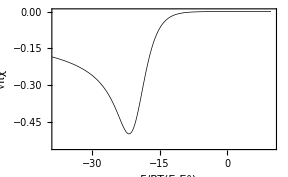

```mathematica
ListPlot[result,PlotRange-> {{-38,10}, { -0.55,0}},optionA2]
```

Fig. Chapter.FigureCaption  Linear sweep voltammogram of an irreversible reaction simulated using eqn (Chapter.EquationNumbered). Simulation parameters: k_s=10^-6 cm · s^-1, υ=1  V · s^-1.

### Chapter.Section.Subsection Functional solution

To solve eqn (Chapter.EquationNumbered) functionally we note that the bracketed term on the right hand side is the same as that given in Chapter 4. We showed that this could be written as the dot product of a matrix Mat and the vector a. Examining the left hand side of eqn (Chapter.EquationNumbered) we begin by expanding it for the first few values of m.

a_1 g_1 d
a_1 g_2 d+a_2 g_2 d
a_1 g_3 d+a_2 g_3 d+a_3 g_3 d
a_1 g_4 d+a_2 g_4 d+a_3 g_4 d+a_4 g_4 d
⋮
a_1 g_m d+a_2 g_m d+⋯+a_(m-1)g_m d+a_m g_m d

The left hand side of eqn (Chapter.EquationNumbered) is the product of the vector a and the lower diagonal matrix Mat2.

Mat2=(g_1 d | 0 | 0 | 0 |   | 0
g_2 d | g_2 d | 0 | 0 |   | 0
g_3 d | g_3 d | g_3 d | 0 |   | 0
g_4 d | g_4 d | g_4 d | g_4 d |   | 0
⋮ |   |   |   |   | ⋮
g_m d | g_m d | g_m d | g_m d | ⋯ | g_m d)

Equation (Chapter.EquationNumbered) can therefore be written as

Mat2·a = 1- Mat·a

or

(Mat2 + Mat)·a = 1

Mat2 can be generated with LowerDiagonalMatrix.

```mathematica
ClearAll[g,mat2,n];

n=4;
mat2=d*LowerDiagonalMatrix[g,n]//MatrixForm
```

(0.125 g[1,1] | 0. | 0. | 0.
0.125 g[2,1] | 0.125 g[2,2] | 0. | 0.
0.125 g[3,1] | 0.125 g[3,2] | 0.125 g[3,3] | 0.
0.125 g[4,1] | 0.125 g[4,2] | 0.125 g[4,3] | 0.125 g[4,4])

The value of g[i,j] for each position in Mat2 can be assigned once a list containing the matrix elements from the bottom row has been generated, for example:

```mathematica
ClearAll[list2];

n=4;
list2=Table[Sqrt[Pi*α*F/(R*T)*υ*𝒟]*Exp[-i*α*Δe]/ki,{i,n}]
```

{3.2393×10^6,2.85867×10^6,2.52277×10^6,2.22634×10^6}

```mathematica
g[r_,_]:=list2⟦r⟧;
n=4;
mat2=α*Δe*LowerDiagonalMatrix[g,n]//MatrixForm
```

(404912. | 0. | 0. | 0.
357334. | 357334. | 0. | 0.
315346. | 315346. | 315346. | 0.
278292. | 278292. | 278292. | 278292.)

Having generated Mat and Mat2, eqn (Chapter.EquationNumbered) can be solved with LinearSolve.

a=LinearSolve[mat+mat2,Table[1.,{n}]];

After solving for a we need to convert these values, that represent the slope at set increments along the dimensionless potential axis, into the dimensionless current χ(b t).

χ=Table[0.,{n}];
χ⟦1⟧=(α*Δe*a⟦1⟧);

This functional method evaluates χ(b t) an order of magnitude faster than the procedural approach outlined in the previous section.
The functional method is detailed in full in the notebook Volterra2.nb.

## Chapter.Section Quasi-reversible reactions - numerical solutions to the Volterra equation

To derive the equation for the cyclic voltammogram for quasi-reversible reactions we begin with (see §5.2)

c_O(0,t)=c_O^*-1/(n F (A(πD_O))^(1/2))∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

and

c_R(0,t)=1/(n F (A(πD_R))^(1/2))∫_0^t (i(τ))/(t-τ)^(1/2)ⅆτ

The current is defined from the Butler-Volmer equation

(i(t))/(n F A)=(D_O((∂c_O(x, t))/(∂x)))_(x=0)=k_s θ^-α exp(ασt)(c_R(0,t)θexp(-σt)-c_O(0,t))

with

θ=exp((n F/R T)(E_i-E°'))

and

σ=(n F/R T)υ

Substituting eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) into (Chapter.EquationNumbered) and extensive rearranging gives

(χ(σ t)(θexp(-σ t))^α)/ψ=1-θ^-1-∫_0^σt (χ(z))/(σt-z)^(1/2)ⅆz-γθexp(-σt)∫_0^(σ t) (χ(z))/(σt-z)^(1/2)ⅆz

where

ψ=k_s/(πσD_O)^(1/2)

and

γ=(D_O/D_R)^(1/2)

To determine a method of solution, after noting that θ^-1 is approximately zero, eqn (Chapter.EquationNumbered) can be simplified to

c_1 χ(σt)(g(σt))^α=1-(1+c_2 g(σt))∫_0^(σ t) (χ(z))/(σt-z)^(1/2)ⅆz

where c_1 and c_2 are constants

c_1=θ^α/ψ

c_2=γθ

Following an analogous procedure used to set up the solution for irreversible reactions and with f_0=0 eqn (Chapter.EquationNumbered) becomes

c_1 g(m d)^α(d∑_(i=1)^m a_i)=1-(1+c_2 g(m d))(h_1 a_m+∑_(i=1)^(m-1) a_i h_(m-i+1))

Substituting the eqn (Chapter.EquationNumbered) into eqn (Chapter.EquationNumbered) gives

c_1 g_m^α h_1 d∑_(i=1)^m a_i=1-(1+c_2 g_m h_1)h_1(a_m+∑_(i=1)^(m-1) a_i((m-i+1)^(3/2)-(m-i)^(3/2)))

with g_m^α=(g(m d))^α/h_1 and g_m=g(m d)/h_1. Equation (Chapter.EquationNumbered) can be written in matrix form as

Mat3·a = 1- (a2 Mat)·a

where

Mat3=(c_1 g_1^α h_1 d | 0 | 0 | 0 |   | 0
c_1 g_2^α h_1 d | c_1 g_2^α h_1 d | 0 | 0 |   | 0
c_1 g_3^α h_1 d | c_1 g_3^α h_1 d | c_1 g_3^α h_1 d | 0 |   | 0
c_1 g_4^α h_1 d | c_1 g_4^α h_1 d | c_1 g_4^α h_1 d | c_1 g_4^α h_1 d |   | 0
⋮ |   |   |   |   | ⋮
c_1 g_m^α h_1 d | c_1 g_m^α h_1 d | c_1 g_m^α h_1 d | c_1 g_m^α h_1 d | ⋯ | c_1 g_m^α h_1 d)

Mat3 is generated in a similar fashion to Mat2 and Mat.

```mathematica
ClearAll[g,d,h1,c1,α];

n=4;
mat3=c1*d*h1*LowerDiagonalMatrix[g^α,n]//MatrixForm
```

(c1 d h1 g^α[1,1] | 0 | 0 | 0
c1 d h1 g^α[2,1] | c1 d h1 g^α[2,2] | 0 | 0
c1 d h1 g^α[3,1] | c1 d h1 g^α[3,2] | c1 d h1 g^α[3,3] | 0
c1 d h1 g^α[4,1] | c1 d h1 g^α[4,2] | c1 d h1 g^α[4,3] | c1 d h1 g^α[4,4])

The term in parenthesis on the right hand side of eqn (Chapter.EquationNumbered) is a matrix generated by multiplying (multiplication not dot product) the matrix Mat by a vector a2.

a2=((1+c_2 g_1 h_1)h_1
(1+c_2 g_2 h_1)h_1
(1+c_2 g_3 h_1)h_1
⋮
(1+c_2 g_(m-1)h_1)h_1
(1+c_2 g_m h_1)h_1)

The vector a2 is generated using Array, for example:

```mathematica
a2=(1+c2*h1*Array[g,4])*h1
```

{h1 (1+c2 h1 g[1]),h1 (1+c2 h1 g[2]),h1 (1+c2 h1 g[3]),h1 (1+c2 h1 g[4])}

Having generated Mat, Mat3 and a2, eqn (Chapter.EquationNumbered) can be solved with LinearSolve.

LinearSolve[mat+a2*mat3,Table[1.,{n}]];

Full implementation is given in the notebook Volterra2.nb.

## Chapter.Section Finite difference solutions for quasi reversible reactions

Chapter.Section.Subsection Introduction

In the previous chapter we defined the dimensionless current as

π^(1/2)χ(σt)=( (D(n-1))/t_n)^(1/2)(3 c_O_1^k-4 c_O_2^k+c_O_3^k)/2

To develop an expression for the dimensionless rate we begin with the Butler Volmer equation:

i(t)=n F A k_s(c_R_1(0,t)exp((1-α)(n F)/(R T)(E-E °'))-c_O_1(0,t)exp(-α(n F)/(R T)(E-E °')))

Dividing both sides by n F A c_O^* (σ D_O)^(1/2) gives:

π^(1/2)χ(σt)=(i(σt))/(n F A c_O^* (σ D_O)^(1/2))= k_s(c_R_1^k ξ^(1-α)-c_O_1^k ξ^-α)

with the dimensionless rate constant is defined as

k_s=k_s/(σD_O)^(1/2)

To simulate quasi-reversible reactions using implicit finite difference methods the surface boundary condition is more complex than those described in the introductory finite difference methods outlined in Chapter 2. For example the fully implicit method requires that a system of equations like those given below must be solved.

-D c_1^(k+1)+(1+2D)c_2^(k+1)-D c_3^(k+1)=c_2^k
-D c_2^(k+1)+(1+2D)c_3^(k+1)-D c_4^(k+1)=c_3^k
-D c_3^(k+1)+(1+2D)c_4^(k+1)-D c_5^(k+1)=c_4^k
⋮
-D c_(j-1)^(k+1)+(1+2D)c_j^(k+1)-D c_(j+1)^(k+1)=c_j^k
⋮
-D c_(m-2)^(k+1)+(1+2D)c_(m-1)^(k+1)=c_(m-1)^k+D c_m^(k+1)

Since D c_1^(k+1) is unknown how do we add it to the column vector on the right hand side? A different approach must be adopted to solve for c_1^(k+1). Combining eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) we have

3 c_O_1^k-4 c_O_2^k+c_O_3^k=2 k_s(c_R_1^k ξ^(1-α)-c_O_1^k ξ^-α)

k_s^*=(k_s( t_n/(D(n-1))))^(1/2)

The concentration of the reduced species, c_R_1^k, is equal to 1-c_O_1^k therefore eqn (Chapter.EquationNumbered) reduces to

3 c_O_1^k-4 c_O_2^k+c_O_3^k=2 k_s^*ξ^(1-α)-2 k_s^*c_O_1^k ξ^(1-α)-2 k_s^*c_O_1^k ξ^-α

Solving eqns (Chapter.EquationNumbered) for c_O_1^k provides the boundary value for simulating a quasi-reversible reaction.

```mathematica
ClearAll[α,ξ,k,Subscript[c, O1],Subscript[c, O2],Subscript[c, O3]];

res=Solve[Subscript[c, O3]-4*Subscript[c, O2]+3*Subscript[c, O1]==2*k*((1-Subscript[c, O1])*ξ^(1-α)-Subscript[c, O1]*ξ^-α),Subscript[c, O1]]
```

{{c_O1→(2 k ξ+4 c_O2 ξ^α-c_O3 ξ^α)/(2 k+2 k ξ+3 ξ^α)}}

The surface boundary value is therefore

c_O_1^k=(2 k_s^*ξ+ξ^α(4 c_O_2^k-c_O_3^k))/(3 ξ^α+2k_s^*(1+ξ))

Substituting eqn (Chapter.EquationNumbered) into the first row of eqn (Chapter.EquationNumbered) gives

```mathematica
ExpandAll[-𝔻*Subscript[c, O1]+(1+2*𝔻)*Subscript[c, O2]-𝔻*Subscript[c, O3]== Subscript[c, O2]^k/.res⟦1⟧]
```

c_O2+2 c_O2 𝔻-c_O3 𝔻-(2 k 𝔻 ξ)/(2 k+2 k ξ+3 ξ^α)-(4 c_O2 𝔻 ξ^α)/(2 k+2 k ξ+3 ξ^α)+(c_O3 𝔻 ξ^α)/(2 k+2 k ξ+3 ξ^α)==c_O2^k

Rearranging the result, after dropping the subscript O, gives

(1+2D-(4 Dξ^α)/(3 ξ^α+2k_s^*(1+ξ)))c_2^(k+1)+(Dξ^α/(3 ξ^α+2k_s^*(1+ξ))-D)c_3^(k+1)=c_2^k+(2 k_s^*Dξ)/(3 ξ^α+2k_s^*(1+ξ))

For k_s^*→∞, 2k_s^*(1+ξ)⩾3 ξ^α and 2k_s^*(1+ξ)⩾4 Dξ^α and the equation for reversible reactions is recovered.

(1+2D)c_2^(k+1)-D c_3^(k+1)=c_2^k+Dξ/(1+ξ)

Equation (Chapter.EquationNumbered) can be written as a series of linear equations:

Y_2 c_2^(k+1)+Z_2 c_3^(k+1)=U_2
X_3 c_2^(k+1)+Y_3 c_3^(k+1)+Z_3 c_4^(k+1)=U_3
⋮
X_j c_(j-1)^(k+1)+Y_j c_j^(k+1)+Z_j c_(j+1)^(k+1)=U_j
⋮
X_(m-1)c_(m-2)^(k+1)+Y_(m-1)c_(m-1)^(k+1)=U_(m-1)

where

X_j=Z_j=-D		for 3≤ j≤m-1

Y_j=1+2D		for 3≤ j≤m-1

U_j=c_j^k		for 3≤ j≤m-1

Y_2=(1+2D-(4 Dξ^α)/(3 ξ^α+2k_s^*(1+ξ)))

Z_2=(Dξ^α/(3 ξ^α+2k_s^*(1+ξ))-D)

U_2=c_2^k+(2 k_s^*Dξ)/(3 ξ^α+2k_s^*(1+ξ))

and

U_(m-1)=c_(m-1)^k+D c_m^(k+1)

For grid expanding in x space only a minor change is necessary (§3.4.3):

```mathematica
ClearAll[a];

ExpandAll[-𝔻*Subscript[c, O1]+(1+(1+a)*𝔻*a^-1)*Subscript[c, O2]-𝔻*a^-1*Subscript[c, O3]== Subscript[c, O2]^k/.res⟦1⟧]
```

c_O2+c_O2 𝔻+(c_O2 𝔻)/a-(c_O3 𝔻)/a-(2 k 𝔻 ξ)/(2 k+2 k ξ+3 ξ^α)-(4 c_O2 𝔻 ξ^α)/(2 k+2 k ξ+3 ξ^α)+(c_O3 𝔻 ξ^α)/(2 k+2 k ξ+3 ξ^α)==c_O2^k

Rearranging the result, after dropping the subscript O, gives

(1+(1+a)D/a-(4 Dξ^α)/(3 ξ^α+2k_s^*(1+ξ)))c_2^(k+1)+(Dξ^α/(3 ξ^α+2k_s^*(1+ξ))-D/a)c_3^(k+1)=c_2^k+(2 k_s^*Dξ)/(3 ξ^α+2k_s^*(1+ξ))

The values of the diagonals are therefore:

X_j=-D a^(4-2j)		for 3≤ j≤m-1

Y_2=(1+(1+a)/a D-(4 Dξ^α)/(3 ξ^α+2k_s^*(1+ξ)))

Y_j=1+(1+a)D a^(3-2j)for 3≤ j≤m-1

Z_2=(D/(3 ξ^α+2k_s^*(1+ξ))-D/a)

Z_j=-Da^(3-2j)		for 3≤ j≤m-1

U_(m-1)=c_(m-1)^k+Da^(5-2m)c_m^(k+1)

and U_2 given by eqn (Chapter.EquationNumbered).
Using a five point approximation for the change in concentration with respect to time X_j and Z_j are given by eqns (Chapter.EquationNumbered), and (Chapter.EquationNumbered) and Y_j and U_j become

Y_j=25/12+2D				for 3≤ j≤m-1

U_j=4 c_j^k-3 c_j^(k-1)+4/3 c_j^(k-2)-1/4 c_j^(k-3) for 3≤ j≤m-1

Y_2=(25/12+2D-(4 Dξ^α)/(3 ξ^α+2k_s^*(1+ξ)))

and

U_2=4 c_2^k-3 c_2^(k-1)+4/3 c_2^(k-2)-1/4 c_2^(k-3)+(2 k_s^*Dξ)/(3 ξ^α+2k_s^*(1+ξ))

For both Richtmyer modification and an expanding space grid X_j and Z_j are given by eqns (Chapter.EquationNumbered), (Chapter.EquationNumbered) and (Chapter.EquationNumbered) for 3≤ j≤ m-1, U_j is given by eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered), and Y_j is

Y_2=(25/12+(1+a)D_2-(4 D_2 ξ^α)/(3 ξ^α+2k_s^*(1+ξ)))

Y_j=25/12+(1+a)D a^(3-2j)		for 3≤ j≤m-1

U_2=4 c_2^k-3 c_2^(k-1)+4/3 c_2^(k-2)-1/4 c_2^(k-3)+(2 k_s^*Dξ)/(3 ξ^α+2k_s^*(1+ξ))

U_j=4 c_j^k-3 c_j^(k-1)+4/3 c_j^(k-2)-1/4 c_j^(k-3)	for 3≤ j≤m-1

Compared to the simulation of a potential step experiment in Chapter 2 the simulation of a cyclic voltammogram requires only a line to state how ξ changes with time. This is left as an exercise for the reader.
Examples are given in the folder SERM/Extra Notebooks/chapter6 that contains notebooks for simulating voltammograms of quasi-reversible reaction using implicit methods with an expanding grid and Richtmyer modification.
Generally it is desirable to use an expanding space grid to reduce the computation time. The coding requires some discussion and this is presented in the next section.

### Chapter.Section.Subsection Implicit finite difference solutions with an expanding grid

To simulate a cyclic voltammogram the diagonal elements Y_2 and Z_2 must be updated at each time increment. We begin by making a list of the diagonal elements.

```mathematica
Clear[makeVarDiagonals];

makeVarDiagonals[m_Integer,d_][a_]:=
	Module[{x,y,z},
		x=Table[-d*a^(4-2*j),{j,3,m-1}];(*lower diagonal*)
		z=Table[-d*a^(3-2*j),{j,2,m-2}];(*upper diagonal*)
		y=Table[1+(1+a)*d*a^(3-2*j),{j,2,m-1}];(*centre*)
{x,y,z}]
```

The the values of y⟦1⟧ and z⟦1⟧ from the lists y and z made using makeVarDiagonals need to be stored separately for further calculations.

y1=First[y]
z1=First[z]

The vector U can be formed by taking either the initial concentration values or the output at each incremental step in the simulation, and dropping the first and last values which correspond to j=1 and j=m values. U_2 and U_(m-1) are then calculated:

(*define ξ at a given time increment i.e.value of k*)
ξ=If[k>(n+1)/2,Exp[upperLimit-region+(τ*k)],Exp[upperLimit-(τ*k)]];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
U=Take[list,{2,m-1}];(*form the vector U*)
U⟦1⟧+=(tmp*𝔻*ksStar*ξ^(1.-α));(*recalculate U_2*)
U⟦-1⟧+=𝔻*a^(5-2*m);(*recalculate U_(m-1)*)

In the code above ksStar is k_s^*and τ is the dimensionless potential increment for each step. The diagonal elements Y_2 and Z_2 are updated, which are positions mat⟦1,1⟧ and mat⟦1,2⟧ in the matrix respectively:

mat⟦1,1⟧=y1-4.*𝔻*tmp;(*recalculate Y_2*)
mat⟦1,2⟧=z1+𝔻*tmp;(*recalculate Z_2*)

Finally eqn (Chapter.EquationNumbered) is solved and new boundary values are added:

tmp2=LinearSolve[mat,u];
(*add boundary values then return the result*)
Flatten[{(ksStar*ξ^(1.-α)+(tmp2⟦1⟧-tmp2⟦2⟧)*4)*tmp,tmp2,1.}]]

These steps can be combined into one function.

ClearAll[solveCV1];

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,u,tmp2},
(*define ξ at a given time increment i.e.value of k*)
ξ=If[k>(n+1)/2,Exp[upperLimit-range+(τ*(k-1))],Exp[upperLimit-(τ*(k-1))]];

tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
u=list[[2;;-2]];(*form the vector U*)
u⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));(*recalculate U_2*)
u⟦-1⟧+=d*a^(5-2*m);(*recalculate U_(m-1)*)
mat⟦1,1⟧=y1-d*tmp*4;(*recalculate Y_2*)
mat⟦1,2⟧=z1+d*tmp;(*recalculate Z_2*)
tmp2=LinearSolve[mat,u];
(*add boundary values then return the result*)
Flatten[{(ksStar*ξ^(1.-α)+(tmp2⟦1⟧-tmp2⟦2⟧)*4)*tmp,tmp2,1.}]];

Using FoldList the complete voltammogram can be simulated by applying solveCV1 beginning with the initial concentration values.
The full program is contained in the notebook implicitCVQuasiExp.nb.
Figures 7.FigureCaption and 7.FigureCaption show a comparison between cyclic voltammograms simulated as described above and data simulated using DigiSim™. note

```mathematica
ClearAll[mke,mkeA,cv2];

mke=Import["logk-3.dat","Table"];
mkeA=convert[mke];
cv2=Import["cv2.dat"];
```

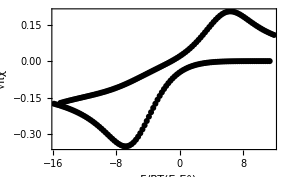

```mathematica
ListPlot[mkeA,optionA,Prolog-> {PointSize[0.015],Black,Point/@cv2}]
```

Fig. Chapter.FigureCaption  Comparison between cyclic voltammograms simulated using DigiSim™ (–––) and the fully implicit method using Mathematica (• • • •). Simulation parameters: k_s=10^-3 cm  · s^-1, υ=1  V · s^-1, D=10^-5 cm^2 ·  s^-1, A=1  cm^2, n=200 and D=2.0.

Next a comparison is made between DigiSim™ data and some Mathematica data for k_s=10^-5 cm ·  s^-1.

```mathematica
ClearAll[mke1,mke1A,cv2a];

mke1=Import["logk-5.dat","Table"];
mke1A=convert[mke1];
cv2a=Import["cv2a.dat"];
```

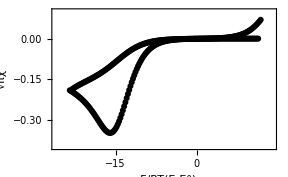

```mathematica
ListPlot[mke1A,optionB,Prolog-> {PointSize[0.015],Black,Point/@cv2a}]
```

Fig. Chapter.FigureCaption  Comparison between cyclic voltammograms simulated using DigiSim™ (–––) and the fully implicit method using Mathematica (• • • •). Simulation parameters: k_s=10^-5 cm  · s^-1, υ=1  V · s^-1, D=10^-5 cm^2 ·  s^-1, A=1  cm^2, n=300 and D=2.0.

## Chapter.Section Summary

In this chapter we have seen how quasi-reversible voltammetric reactions can be solved symbolically and numerically in Mathematica. In the next two chapters we apply these methods to ac and pulse voltammetric methods.

## Further Reading

Britz, D. (1988). Digital Simulation in Electrochemistry, Springer-Verlag, Berlin.
Nicholson, R. S. and Shain, I. (1964). Analytical Chemistry, 36, 704-23.
Nicholson, R. S. (1965). Analytical Chemistry, 37, 1351-5.
Nicholson, R. S. and Olmstead, M. L. (1972). Numerical Solution of Integral Equations. In Electrochemistry; Calculations, Simulations, and Instrumentation, (eds. J. S. Mattson, H. B. Mark jnr., and H. C. MacDonald jnr.), pp. 119-38. Marcel Dekker, New York.
Press, W. H., Teukolsky, S. A., Vetterling, W. T., and Flannery, B. P. (1992). Numerical Recipes in C, (2nd edn). Cambridge University Press, New York.
Rudolph, M. (1995). Digital Simulations with Fast Implicit Finite Difference Algorithm: The Development of a General Simulator for Electrochemical Processes. In Physical Electrochemistry; Principles, Methods, and Applications, (ed. I. Rubenstein), pp. 81-130. Marcel Dekker, New York.
Rudolph, M. (1992). Journal of Electroanalytical Chemistry, 338, 85-98.